```mathematica
(*Simulations using linear programming and noisy data, exploring corasening strategies*)

mat[pop_,samp_]:=Table[Binomial[i,j]Binomial[pop-i,samp-j],{j,0,samp},{i,0,pop}]/Binomial[pop,samp]
```

```mathematica
(*Start with regular LP, but coarsen the last few bins (to see how much info  we loose) Here we are still assuming infinite data!*)



extrapolateCoarse[sampsize_,popsize_,max_,cut_]:=Module[{b,tot},totsnp=5000;
pop={Table[10/(n+1/10),{n,0,max}]};
pop=pop/Apply[Plus,Flatten[pop]]*totsnp;
If[popsize==sampsize,(*Then project down rather than extrapolate.*)
bloc=mat[max,popsize];
poploc=pop;
sub=Transpose[Dot[bloc,Transpose[poploc]]]; 


tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];

If[popsize<sampsize,  (*Then project down rather than extrapolate.*)  b=mat[max,sampsize];
bchp=b[[2;;,2;;]];
bloc=mat[sampsize,popsize];
poploc=Transpose[Dot[b,Transpose[pop]]]; 

sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];


b=mat[max,popsize];


bloc=mat[popsize,sampsize];
(*projection matrix without singletons*)
bchp=bloc[[2;;,2;;]];
poploc=Transpose[Dot[b,Transpose[pop]]];
sub=Transpose[Dot[bloc,Transpose[poploc]]];
start=Apply[Plus, sub⟦1,2;;⟧];
exact=Apply[Plus, poploc⟦1,2;;⟧];
subcoarse=sub[[1]][[1;;cut+1]];
AppendTo[subcoarse,Apply[Plus,sub[[1]][[cut+2;;]]]];

bchpCoarse=bchp[[1;;cut+1,1;;]];
bchpCoarse[[cut+1,1;;]]=Apply[Plus,bchp[[cut+1;;,1;;]]];
 
(*pop={Table[10/(n+1/10),{n,0,popsize}]};

sub=Transpose[Dot[b,Transpose[pop]]];*)
c=Table[1,{i,1,popsize}];
sol=LinearProgramming[c,bchpCoarse,N[Table[{subcoarse[[i+1]],0},{i,1,cut+1}],100],Method->"RevisedSimplex"];

solmin=LinearProgramming[-c,bchpCoarse,N[Table[{subcoarse[[i+1]],0},{i,1,cut+1}],100],Method->"RevisedSimplex"];

Return[{start, exact,c.sol,c.solmin}]



]
```

```mathematica
(*Explore convergence of linear programming converges as a function of number of bins used*)
nstart=50
nend=200
maxbins=20
output=ParallelTable[Timing[N[extrapolateCoarse[nstart,nend,nend,i]]],{i,1,maxbins}]
```

50

200

20

{{0.47592,{1410.56,1820.36,1501.52,2323.14}},{0.49766,{1410.56,1820.36,1629.59,2157.55}},{0.56241,{1410.56,1820.36,1664.84,1979.85}},{0.59012,{1410.56,1820.36,1715.57,1941.46}},{0.64586,{1410.56,1820.36,1732.16,1891.42}},{0.69069,{1410.56,1820.36,1751.91,1877.6}},{0.7796,{1410.56,1820.36,1758.2,1857.6}},{0.79192,{1410.56,1820.36,1782.46,1851.23}},{0.87741,{1410.56,1820.36,1789.8,1843.23}},{0.8535,{1410.56,1820.36,1800.71,1838.82}},{0.95227,{1410.56,1820.36,1803.98,1833.46}},{1.00692,{1410.56,1820.36,1809.06,1831.71}},{1.18437,{1410.56,1820.36,1811.03,1829.15}},{1.18319,{1410.56,1820.36,1813.52,1828.25}},{1.3904,{1410.56,1820.36,1814.39,1826.89}},{1.40031,{1410.56,1820.36,1815.64,1826.31}},{1.50079,{1410.56,1820.36,1816.36,1825.02}},{1.40676,{1410.56,1820.36,1817.33,1824.42}},{1.49697,{1410.56,1820.36,1817.75,1823.36}},{1.41891,{1410.56,1820.36,1818.3,1822.92}}}

2115.18

1410.56

1820.36

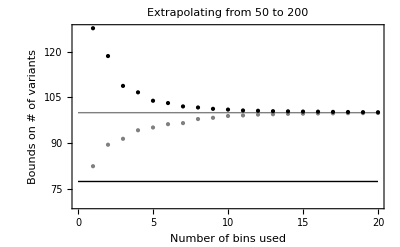

```mathematica
true=N[Apply[Plus,poploc[[1,2;;]]]]

start=output[[1,2,1]]
exact=output[[1,2,2]]
true=exact;

ListPlot[{output[[1;;,2,3]]100 /exact,output[[1;;,2,4]]100/exact},Joined->False,PlotStyle->{Gray,Black},Epilog->{Gray,Line[{{0,100},{maxbins,100}}],Black,Line[{{0,start*100/exact},{maxbins,start*100/exact}}]},Frame->{True,True,False,False},FrameLabel->{"Number of bins used","Bounds on # of variants"},PlotLabel->"Extrapolating from "<>ToString[nstart]<>" to "<>ToString[nend] ,PlotRange->{0.9 start *100/exact,All}]
```

```mathematica
(*Coarsen by keeping the first d bins. then use the following 2,4,8, etc *)
coarsenSFS[sfs_,cut_]:=Module[{temp,max,curr,d},temp=sfs[[1]][[1;;cut+1]];max=cut+1;d=1;curr=max;While[max<Length[sfs[[1]]],max+=2^d;d+=1;AppendTo[temp,Apply[Plus,sfs[[1]][[(curr+1);;Min[max,Length[sfs[[1]]]]]]]];curr=max
];temp]
coarsenMAT[mat_,cut_]:=Module[{max,temp,d,curr},temp=mat[[1;;cut,1;;]];;max=cut;d=1;curr=max;While[max<Length[mat],max+=2^d;d+=1;AppendTo[temp,Apply[Plus,mat[[(curr+1);;Min[max,Length[mat]]]]]];curr=max
];temp]

extrapolateCoarse2[sampsize_,popsize_,max_,cut_]:=Module[{b,tot,bchpcoarse},totsnp=5000;
pop={Table[10/(n+1/10),{n,0,max}]};
pop=pop/Apply[Plus,Flatten[pop]]*totsnp;
If[popsize==sampsize,(*Then project down rather than extrapolate.*)
bloc=mat[max,popsize];
poploc=pop;
sub=Transpose[Dot[bloc,Transpose[poploc]]]; 


tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];

If[popsize<sampsize,  (*Then project down rather than extrapolate.*)  b=mat[max,sampsize];
bchp=b[[2;;,2;;]];
bloc=mat[sampsize,popsize];
poploc=Transpose[Dot[b,Transpose[pop]]]; 

sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];


b=mat[max,popsize];


bloc=mat[popsize,sampsize];
(*projection matrix without singletons*)
bchp=bloc[[2;;,2;;]];
poploc=Transpose[Dot[b,Transpose[pop]]];
sub=Transpose[Dot[bloc,Transpose[poploc]]];
subcoarse=coarsenSFS[sub,cut];


bchpcoarse=coarsenMAT[bchp,cut];

 
(*pop={Table[10/(n+1/10),{n,0,popsize}]};

sub=Transpose[Dot[b,Transpose[pop]]];*)
c=Table[1,{i,1,popsize}];
sol=LinearProgramming[c,bchpcoarse,N[Table[{subcoarse[[i]],0},{i,2,Length[subcoarse]}],100],Method->"RevisedSimplex"];

solmin=LinearProgramming[-c,bchpcoarse,N[Table[{subcoarse[[i]],0},{i,2,Length[subcoarse]}],100],Method->"RevisedSimplex"];

Return[{Length[bchpcoarse],c.sol,c.solmin}]



]
```

```mathematica
(*Now, add some Poisson noise. Returns an error when no solution is found*)

extrapolatePoisson[sampsize_,popsize_,max_,cut_]:=Module[{b,tot,poisson},totsnp=500000;
pop={Table[10/(n+1/10),{n,0,max}]};
pop=pop/Apply[Plus,Flatten[pop]]*totsnp;
If[popsize==sampsize,(*Then project down rather than extrapolate.*)
bloc=mat[max,popsize];
poploc=pop;
sub=Transpose[Dot[bloc,Transpose[poploc]]]; 


tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];

If[popsize<sampsize,  (*Then project down rather than extrapolate.*)  b=mat[max,sampsize];
bchp=b[[2;;,2;;]];
bloc=mat[sampsize,popsize];
poploc=Transpose[Dot[b,Transpose[pop]]]; 

sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];


b=mat[max,popsize];


bloc=mat[popsize,sampsize];
(*projection matrix without singletons*)
bchp=bloc[[2;;,2;;]];
poploc=Transpose[Dot[b,Transpose[pop]]];
sub=Transpose[Dot[bloc,Transpose[poploc]]];
(*Build maximum likelihood solution with noise*)
poisson=Map[RandomInteger[PoissonDistribution[#]]&,sub[[1]]];

subcoarse=poisson[[1;;cut+1]];
AppendTo[subcoarse,Apply[Plus,poisson[[cut+2;;]]]];

bchpCoarse=bchp[[1;;cut+1,1;;]];
bchpCoarse[[cut+1,1;;]]=Apply[Plus,bchp[[cut+1;;,1;;]]];
 
(*pop={Table[10/(n+1/10),{n,0,popsize}]};

sub=Transpose[Dot[b,Transpose[pop]]];*)
c=Table[1,{i,1,popsize}];
sol=Check[c.LinearProgramming[c,bchpCoarse,N[Table[{subcoarse[[i+1]],0},{i,1,cut+1}],100],Method->"RevisedSimplex"],"Err"];

solmin=Check[c.LinearProgramming[-c,bchpCoarse,N[Table[{subcoarse[[i+1]],0},{i,1,cut+1}],100],Method->"RevisedSimplex"],"Err"];

Return[{sol,Apply[Plus,poploc[[1,2;;]]],solmin}]



]
```

```mathematica
output=ParallelTable[N[extrapolatePoisson[50,500,500,i]],{i,1,8}]
```

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

{{144695.,199511.,398669.},{159270.,199511.,341910.},{163565.,199511.,278676.},{169203.,199511.,260251.},{175518.,199511.,250547.},{180006.,199511.,237729.},{Err,199511.,Err},{187265.,199511.,228072.}}

```mathematica
(*Now we want to perform a bootstrap using our sample. So we will generate Poisson sample of our poisson sample (as a Pseudo bootstrap)*)

extrapolateBoot[sampsize_,popsize_,max_,cut_,nboot_]:=Module[{b,tot},totsnp=1000000;
pop={Table[10/(n+1/10),{n,0,max}]};
pop=pop/Apply[Plus,Flatten[pop]]*totsnp;
If[popsize==sampsize,(*Then project down rather than extrapolate.*)
bloc=mat[max,popsize];
poploc=pop;
sub=Transpose[Dot[bloc,Transpose[poploc]]]; 


tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];

If[popsize<sampsize,  (*Then project down rather than extrapolate.*)  
b=mat[max,sampsize];
bchp=b[[2;;,2;;]];
bloc=mat[sampsize,popsize];
poploc=Transpose[Dot[b,Transpose[pop]]]; 

sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];


b=mat[max,popsize];


bloc=mat[popsize,sampsize];
(*projection matrix without singletons*)
bchp=bloc[[2;;,2;;]];
poploc=Transpose[Dot[b,Transpose[pop]]];
sub=Transpose[Dot[bloc,Transpose[poploc]]];
(*Build maximum likelihood solution with noise*)
poisson=Map[RandomInteger[PoissonDistribution[#]]&,sub[[1]]];

subcoarse=poisson[[1;;cut+1]];

AppendTo[subcoarse,Apply[Plus,poisson[[cut+2;;]]]];
obs=Apply[Plus,subcoarse[[2;;]]];
bchpCoarse=bchp[[1;;cut+1,1;;]];
bchpCoarse[[cut+1,1;;]]=Apply[Plus,bchp[[cut+1;;,1;;]]];
Print["Total number of bins "<>ToString[Dimensions[bchpCoarse][[1]]]];
 
(*pop={Table[10/(n+1/10),{n,0,popsize}]};

sub=Transpose[Dot[b,Transpose[pop]]];*)
c=Table[1,{i,1,popsize}];
sol=Check[c.LinearProgramming[c,bchpCoarse,N[Table[{subcoarse[[i+1]],0},{i,1,cut+1}],100],Method->"RevisedSimplex"],"Err"];

solmin=Check[c.LinearProgramming[-c,bchpCoarse,N[Table[{subcoarse[[i+1]],0},{i,1,cut+1}],100],Method->"RevisedSimplex"],"Err"];
exact=Apply[Plus,poploc[[1,2;;]]];
ret1={obs,sol,exact,solmin};
boots={};
For[i=1,i≤nboot,i++,
poissonBoot=Map[RandomInteger[PoissonDistribution[#]]&,poisson];
subcoarse=poissonBoot[[1;;cut+1]];
AppendTo[subcoarse,Apply[Plus,poissonBoot[[cut+2;;]]]];

bchpCoarse=bchp[[1;;cut+1,1;;]];
bchpCoarse[[cut+1,1;;]]=Apply[Plus,bchp[[cut+1;;,1;;]]];
 
(*pop={Table[10/(n+1/10),{n,0,popsize}]};

sub=Transpose[Dot[b,Transpose[pop]]];*)
c=Table[1,{i,1,popsize}];
sol=Check[c.LinearProgramming[c,bchpCoarse,N[Table[{subcoarse[[i+1]],0},{i,1,cut+1}],100],Method->"RevisedSimplex"],0];

solmin=Check[c.LinearProgramming[-c,bchpCoarse,N[Table[{subcoarse[[i+1]],0},{i,1,cut+1}],100],Method->"RevisedSimplex"],1000*exact];

AppendTo[boots,{sol,solmin}];
];



Return[{ret1,boots}]
]

(*Same as above, but we use the exponential coarsening strategy.*)
extrapolateBoot2[sampsize_,popsize_,max_,cut_,nboot_]:=Module[{b,tot},totsnp=1000000;
pop={Table[10/(n+1/10),{n,0,max}]};
pop=pop/Apply[Plus,Flatten[pop][[2;;]]]*totsnp;
If[popsize==sampsize,(*Then project down rather than extrapolate.*)
bloc=mat[max,popsize];
poploc=pop;
sub=Transpose[Dot[bloc,Transpose[poploc]]]; 


tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];

If[popsize<sampsize,  (*Then project down rather than extrapolate.*)  
b=mat[max,sampsize];
bchp=b[[2;;,2;;]];
bloc=mat[sampsize,popsize];
poploc=Transpose[Dot[b,Transpose[pop]]]; 

sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];


b=mat[max,popsize];


bloc=mat[popsize,sampsize];
(*projection matrix without singletons*)
bchp=bloc[[2;;,2;;]];
poploc=Transpose[Dot[b,Transpose[pop]]];
sub=Transpose[Dot[bloc,Transpose[poploc]]];
(*Build maximum likelihood solution with noise*)
poisson=Map[RandomInteger[PoissonDistribution[#]]&,sub[[1]]];

(*subcoarse=poisson[[1;;cut+1]];*)
subcoarse=coarsenSFS[{poisson}, cut];
bchpCoarse=coarsenMAT[bchp,cut];
Print["Total number of bins "<>ToString[Length[subcoarse]-1]];

obs=Apply[Plus,subcoarse[[2;;]]];

 
(*pop={Table[10/(n+1/10),{n,0,popsize}]};

sub=Transpose[Dot[b,Transpose[pop]]];*)
c=Table[1,{i,1,popsize}];


sol=Check[c.LinearProgramming[c,bchpCoarse,N[Table[{subcoarse[[i]],0},{i,2,Length[subcoarse]}],100],Method->"RevisedSimplex"],"Err"];

solmin=Check[c.LinearProgramming[-c,bchpCoarse,N[Table[{subcoarse[[i]],0},{i,2,Length[subcoarse]}],100],Method->"RevisedSimplex"],"Err"];

exact=Apply[Plus,poploc[[1,2;;]]];
ret1={obs,sol,exact,solmin};

boots={};
For[i=1,i≤nboot,i++,
poissonBoot=Map[RandomInteger[PoissonDistribution[#]]&,poisson];

subcoarse=coarsenSFS[{poissonBoot}, cut];


c=Table[1,{i,1,popsize}];

sol=Check[c.LinearProgramming[c,bchpCoarse,N[Table[{subcoarse[[i]],0},{i,2,Length[subcoarse]}],100],Method->"RevisedSimplex"],0];

solmin=Check[c.LinearProgramming[-c,bchpCoarse,N[Table[{subcoarse[[i]],0},{i,2,Length[subcoarse]}],100],Method->"RevisedSimplex"],1000*exact];

AppendTo[boots,{sol,solmin}];
];



Return[{ret1,boots}]
]
```

```mathematica
(*get a confidence interval from the output!*)
confInt[out_]:=Module[{start,exact,max,min},start=out[[1,1]];exact=out[[1,3]]; minmin=Quantile[out[[2,1;;,1]],0.025]; minmax=Quantile[out[[2,1;;,1]],0.975];maxmax=Quantile[out[[2,1;;,2]],.975];maxmin=Quantile[out[[2,1;;,2]],.025];{start,exact,minmin,minmax,maxmin,maxmax}]
```

```mathematica
(*Exponential coarsening strategy*)
out=ParallelTable[N[extrapolateBoot[50,100,100,cut,20]],{cut,1,10}];
out2=ParallelTable[N[extrapolateBoot2[50,100,100,cut,20]],{cut,1,10}];
```

Total number of bins 8

Total number of bins 11

Total number of bins 6

Total number of bins 10

Total number of bins 7

Total number of bins 9

Total number of bins 12

Total number of bins 13

Total number of bins 14

Total number of bins 15

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

```mathematica
(*"hard cap" coarsening strategy*)
```

Total number of bins 6

Total number of bins 4

Total number of bins 7

Total number of bins 2

Total number of bins 3

Total number of bins 5

Total number of bins 8

Total number of bins 9

Total number of bins 10

Total number of bins 11

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

```mathematica
plotData=Map[confInt,out[[1;;8]]];
plotData2=Map[confInt,out2[[1;;8]]]/1000000;
out2[[9]]
```

{{872887.,998701.,1.×10^6,999097.},{{997148.,997463.},{1.00056×10^6,1.00067×10^6},{1.00178×10^6,1.00204×10^6},{998172.,998509.},{999760.,999985.},{1.0005×10^6,1.00088×10^6},{997479.,997867.},{998620.,998899.},{998609.,998967.},{998659.,999018.},{999019.,999373.},{998051.,998393.},{998972.,999095.},{997430.,997702.},{997727.,998059.},{999752.,1.00014×10^6},{1.0006×10^6,1.00097×10^6},{998426.,998798.},{998882.,999210.},{999686.,999920.}}}

{{873869.,1.00058×10^6,1.×10^6,1.00095×10^6},{{1.00008×10^6,1.00041×10^6},{1.00117×10^6,1.00151×10^6},{1.00329×10^6,1.00362×10^6},{996730.,997111.},{1.00108×10^6,1.00147×10^6},{1.00182×10^6,1.00222×10^6},{1.0006×10^6,1.00099×10^6},{1.00222×10^6,1.00255×10^6},{1.00114×10^6,1.00149×10^6},{998225.,998576.},{1.00001×10^6,1.00037×10^6},{998980.,999330.},{0.,1.×10^9},{996337.,996649.},{999827.,999953.},{1.00092×10^6,1.00131×10^6},{1.00009×10^6,1.00036×10^6},{1.00181×10^6,1.00216×10^6},{997746.,998125.},{1.00036×10^6,1.00073×10^6}}}

```mathematica
h=Graphics[Line[{{0,-.02},{0,.02}}]];
h1=Graphics[Line[.15*{{-1,1/2},{0,0},{-1,-1/2},{-1,1/2}}]];
arrstylelow=Arrowheads[{{.1,0,{h1,.01}},{.1,1,{h,.01}}}];
arrstyleup=Arrowheads[{{-.1,1,{h1,.01}},{.1,0,{h,.01}}}];
barsmin=Table[{arrstylelow, Arrow[{{i,plotData[[i,3]]}, {i,plotData[[i,4]]}}]},{i,1,Length[plotData]}];
barsmax=Table[{arrstyleup,Arrow[{{i,plotData[[i,5]]}, {i,plotData[[i,6]]}}]},{i,1,Length[plotData]}];

Plot[{plotData[[1,2]],plotData[[1,1]]},{x,1,Length[plotData]},Epilog->Join[barsmin,barsmax],PlotRange->{250000,400000},PlotStyle->{Black,{Dashed,Black}},Frame->{True,True,False,False},FrameLabel->{"Number of bins used","Predicted and observed counts" },PlotLabel->"Regular bins"]



barsmin2=Table[{arrstylelow, Arrow[{{i,plotData2[[i,3]]}, {i,plotData2[[i,4]]}}]},{i,1,Length[plotData2]}];
barsmax2=Table[{arrstyleup,Arrow[{{i,plotData2[[i,5]]}, {i,plotData2[[i,6]]}}]},{i,1,Length[plotData2]}];

lpbybin=Plot[{plotData2[[1,2]],plotData2[[1,1]]},{x,1,Length[plotData2]},Epilog->{Join[barsmin2,barsmax2],Style[Text["Observed",{6,1.01*plotData2[[1,1]]}],13],Style[Text["Exact and predicted",{6,1.03*plotData2[[1,2]]}],13]}  ,PlotRange->{.85,1.06},PlotStyle->{Black,{Dashed,Black}},Frame->{True,True,False,False},FrameStyle->Directive[13],FrameLabel->{"p: Number of bins treated exactly","Predicted and observed counts (Millions)" },PlotLabel->"Exponential bins"]
```

Part::partd: Part specification plotData ⟦ 1, 2 ⟧ is longer than depth of object.

Part::partd: Part specification plotData ⟦ 1, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

-Graphics-

Part::partd: Part specification plotData2 ⟦ 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification plotData2 ⟦ 1, 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

-Graphics-

```mathematica
Export["~/Dropbox/capture_recapture/figures/lpbybin.pdf",lpbybin]
Export["~/Dropbox/capture_recapture/figures/lpbybin.eps",lpbybin]
```

~/Dropbox/capture_recapture/figures/lpbybin.pdf

~/Dropbox/capture_recapture/figures/lpbybin.eps

```mathematica
(*Now test for fixed number of bins as a function of number of SNPs*)
```

```mathematica
extrapolateBootVarTot[sampsize_,popsize_,max_,cut_,nboot_,totsnp_]:=Module[{b,tot},
pop={Table[10/(n+1/10),{n,0,max}]};
pop=pop/Apply[Plus,Flatten[pop][[2;;]]]*totsnp;
If[popsize==sampsize,(*Then project down rather than extrapolate.*)
bloc=mat[max,popsize];
poploc=pop;
sub=Transpose[Dot[bloc,Transpose[poploc]]]; 


tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];

If[popsize<sampsize,  (*Then project down rather than extrapolate.*)  
b=mat[max,sampsize];
bchp=b[[2;;,2;;]];
bloc=mat[sampsize,popsize];
poploc=Transpose[Dot[b,Transpose[pop]]]; 

sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];


b=mat[max,popsize];


bloc=mat[popsize,sampsize];
(*projection matrix without singletons*)
bchp=bloc[[2;;,2;;]];
poploc=Transpose[Dot[b,Transpose[pop]]];
sub=Transpose[Dot[bloc,Transpose[poploc]]];
(*Build maximum likelihood solution with noise*)
poisson=Map[RandomInteger[PoissonDistribution[#]]&,sub[[1]]];

(*subcoarse=poisson[[1;;cut+1]];*)
subcoarsePoiss=coarsenSFS[{poisson}, cut];
subcoarse=coarsenSFS[{sub⟦1⟧}, cut];
bchpCoarse=coarsenMAT[bchp,cut];
Print["Total number of bins "<>ToString[Length[subcoarsePoiss]-1]];

obs=Apply[Plus,subcoarsePoiss[[2;;]]];

 
(*pop={Table[10/(n+1/10),{n,0,popsize}]};

sub=Transpose[Dot[b,Transpose[pop]]];*)
c=Table[1,{i,1,popsize}];


sol=Check[c.LinearProgramming[c,bchpCoarse,N[Table[{subcoarsePoiss[[i]],0},{i,2,Length[subcoarse]}],100],Method->"RevisedSimplex"],"Err"];

solmin=Check[c.LinearProgramming[-c,bchpCoarse,N[Table[{subcoarsePoiss[[i]],0},{i,2,Length[subcoarse]}],100],Method->"RevisedSimplex"],"Err"];

exact=Apply[Plus,poploc[[1,2;;]]];
ret1={obs,sol,exact,solmin};

boots={};
For[i=1,i≤nboot,i++,
poissonBoot=Map[RandomInteger[PoissonDistribution[#]]&,poisson];

subcoarse=coarsenSFS[{poissonBoot}, cut];


c=Table[1,{i,1,popsize}];

sol=Check[c.LinearProgramming[c,bchpCoarse,N[Table[{subcoarse[[i]],0},{i,2,Length[subcoarse]}],100],Method->"RevisedSimplex"],0];

solmin=Check[c.LinearProgramming[-c,bchpCoarse,N[Table[{subcoarse[[i]],0},{i,2,Length[subcoarse]}],100],Method->"RevisedSimplex"],1000*exact];

AppendTo[boots,{sol,solmin}];
];



Return[{ret1,boots}]
]
```

```mathematica
sizes=Table[10^nsnp,{nsnp,4,10}]
```

{10000,100000,1000000,10000000,100000000,1000000000,10000000000}

```mathematica
(*This step is a bit slower, because we are performing bootstrap over a wide range of difficult extrapolations*)
start=50
target=500
max=500
cut=10
nboot=20

outS=ParallelTable[N[Check[extrapolateBootVarTot[start,target,max,cut,nboot,10^nsnp],
Check[extrapolateBootVarTot[start,target,max,cut,nboot,10^nsnp],
Check[extrapolateBootVarTot[start,target,max,cut-1,nboot,10^nsnp],
Check[extrapolateBootVarTot[start,target,max,cut-2,nboot,10^nsnp],
Check[extrapolateBootVarTot[start,target,max,cut-3,nboot,10^nsnp],
Check[extrapolateBootVarTot[start,target,max,cut-4,nboot,10^nsnp],
Check[extrapolateBootVarTot[start,target,max,cut-5,nboot,10^nsnp],
Check[extrapolateBootVarTot[start,target,max,cut-6,nboot,10^nsnp],
extrapolateBootVarTot[start,target,max,cut-7,nboot,10^nsnp]]]]]]]]]],{nsnp,4,10}];
```

50

500

500

10

20

Total number of bins 15

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

Total number of bins 15

Total number of bins 15

Total number of bins 15

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

Total number of bins 15

Total number of bins 15

Total number of bins 15

Total number of bins 14

Total number of bins 14

Total number of bins 14

Total number of bins 13

Total number of bins 13

Total number of bins 12

Total number of bins 13

Total number of bins 12

Total number of bins 11

Total number of bins 15

Total number of bins 10

Total number of bins 11

Total number of bins 9

Total number of bins 15

Total number of bins 15

Total number of bins 8

Total number of bins 15

Total number of bins 15

Total number of bins 14

Total number of bins 15

Total number of bins 14

Total number of bins 14

Total number of bins 13

Total number of bins 13

Total number of bins 12

Total number of bins 12

Total number of bins 11

Total number of bins 11

Total number of bins 10

```mathematica
plotDataS=Map[confInt,outS[[1;;7]]]/1000000;
```

```mathematica
plotDataS
```

{{0.006631,0.01,0.00793061,0.00882367,0.0108934,0.0139356},{0.067528,0.1,0.0891692,0.104581,0.112911,0.135656},{0.672826,1.,0.879114,1.18496,1.01588,1.23441},{6.72962,10.,9.04855,9.38526,11.5087,11.8454},{67.274,100.,90.6685,95.3731,103.697,113.205},{672.673,1000.,921.206,1007.93,1066.38,1116.86},{6726.79,10000.,9277.19,9615.86,10537.1,10958.1}}

```mathematica
barsmin2=Table[{arrstylelow, Arrow[{{Log10[sizes⟦i⟧],plotDataS[[i,3]]/plotDataS[[i,2]]}, {Log10[sizes⟦i⟧],plotDataS[[i,4]]/plotDataS[[i,2]]}}]},{i,1,Length[plotDataS]}];
barsmax2=Table[{arrstyleup,Arrow[{{Log10[sizes⟦i⟧],plotDataS[[i,5]]/plotDataS[[i,2]]}, {Log10[sizes⟦i⟧],plotDataS[[i,6]]/plotDataS[[i,2]]}}]},{i,1,Length[plotDataS]}];
```

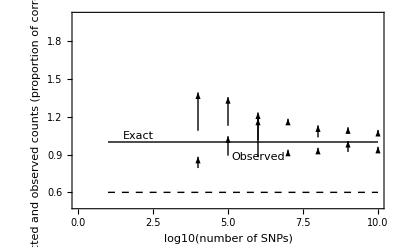

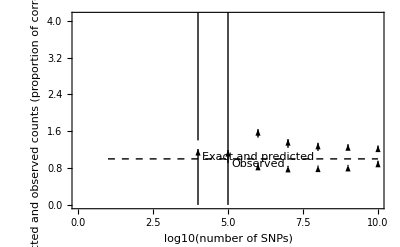

```mathematica
ListPlot[{Table[{x,1},{x,1,10}],Table[{x,.6},{x,1,10}]},Joined->True,Epilog->{Join[barsmin2,barsmax2],Style[Text["Observed",{6,1.01*plotData2[[1,1]]}],13],Style[Text["Exact",{2,1.05*plotData2[[1,2]]}],13]}  ,PlotRange->{.5,2},PlotStyle->{Black,{Dashed,Black}},Frame->{True,True,False,False},FrameStyle->Directive[13],FrameLabel->{"log10(number of SNPs)","Predicted and observed counts (proportion of correct value)" }]
```

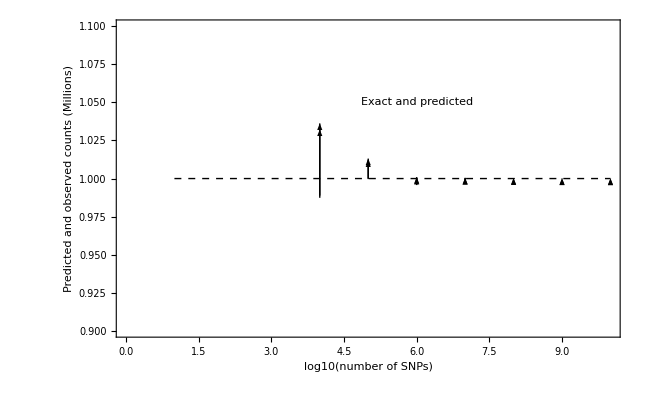

```mathematica
(*extrapolate 50 to 100--not that many counts needed!*)
```

```mathematica
HGDownsample[pop_,to_]:=Module[{curr,from,ls,i},from=Length[pop]-1;curr=Table[0,{i,1,to+1}];
For [i=1 (*no need to do zeros!*),i≤from-1 (*no need to do fulls*),i++,ls=Tally[RandomVariate[HypergeometricDistribution[to,i+1,from],pop⟦i+1⟧]]; Map[curr⟦#⟦1⟧+1⟧+=#⟦2⟧&,ls]];curr⟦1⟧+=pop⟦1⟧;curr⟦-1⟧+=pop⟦-1⟧;Return[curr]  ]


(*Simulation for the effect of finite data: Take a smooth SFS; Poisson Random field sample it; for each SNP in the set and each bootstrap iteration; actually perform a Hypergeometric downsampling.*)
extrapolateBootHypergeo[sampsize_,popsize_,max_,cut_,nboot_,totsnp_]:=Module[{b,tot},
pop={Table[10/(n+1/10),{n,0,max}]};
pop=pop/Apply[Plus,Flatten[pop][[2;;]]]*totsnp;
(*now poissonify*)
poisson={Map[RandomInteger[PoissonDistribution[#]]&,pop[[1]]]};

If[popsize==sampsize,(*Then project down rather than extrapolate.*)
bloc=mat[max,popsize];
poploc=poisson;
sub=Transpose[Dot[bloc,Transpose[poploc]]]; 


tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];

If[popsize<sampsize,  (*Then project down rather than extrapolate.*)  
b=mat[max,sampsize];
bchp=b[[2;;,2;;]];
bloc=mat[sampsize,popsize];
poploc=Transpose[Dot[b,Transpose[poisson]]]; 

sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];


b=mat[max,popsize];


bloc=mat[popsize,sampsize];
(*projection matrix without singletons*)
bchp=bloc[[2;;,2;;]];
(*I have a finite genome, and currently a possible float as the numer*)
poploc=Round[Transpose[Dot[b,Transpose[poisson]]]];
sub=HGDownsample[poploc⟦1⟧,sampsize];
(*Build maximum likelihood solution with noise*)


(*subcoarse=poisson[[1;;cut+1]];*)
subcoarse=coarsenSFS[{sub}, cut];
bchpCoarse=coarsenMAT[bchp,cut];


obs=Apply[Plus,subcoarse[[2;;]]];

 
(*pop={Table[10/(n+1/10),{n,0,popsize}]};

sub=Transpose[Dot[b,Transpose[pop]]];*)
c=Table[1,{i,1,popsize}];


sol=Check[c.LinearProgramming[c,bchpCoarse,N[Table[{subcoarse[[i]],0},{i,2,Length[subcoarse]}],100],Method->"RevisedSimplex"],"Err"];

solmin=Check[c.LinearProgramming[-c,bchpCoarse,N[Table[{subcoarse[[i]],0},{i,2,Length[subcoarse]}],100],Method->"RevisedSimplex"],"Err"];

exact=Apply[Plus,poploc[[1,2;;]]];
ret1={obs,sol,exact,solmin};

boots={};
For[i=1,i≤nboot,i++,
sub=HGDownsample[poploc⟦1⟧,sampsize];;

subcoarse=coarsenSFS[{sub}, cut];


c=Table[1,{i,1,popsize}];

sol=Check[c.LinearProgramming[c,bchpCoarse,N[Table[{subcoarse[[i]],0},{i,2,Length[subcoarse]}],100],Method->"RevisedSimplex"],0];

solmin=Check[c.LinearProgramming[-c,bchpCoarse,N[Table[{subcoarse[[i]],0},{i,2,Length[subcoarse]}],100],Method->"RevisedSimplex"],1000*exact];

AppendTo[boots,{sol,solmin}];
];



Return[{ret1,boots}]
]
```

```mathematica
N[poploc]
```

{{174085.,14566.1,7426.96,4968.79,3723.75,2970.4,2470.16,2117.05,1854.52,1650.82,1488.26,1356.4,1248.09,1157.67,1080.54,1013.24,953.311,899.171,849.824,804.679,763.393,725.749,691.545,660.535,632.401,606.782,583.311,561.663,541.575,522.845,505.319,488.873,473.401,458.808,445.017,431.968,419.619,407.944,396.923,386.538,376.761,367.555,358.871,350.653,342.841,335.38,328.226,321.352,314.748,308.418,302.377,296.64,291.214,286.095,281.269,276.71,272.39,268.279,264.349,260.564,256.883,253.255,249.618,245.912,242.089,238.123,234.017,229.807,225.556,221.338,217.227,213.276,209.513,205.933,202.51,199.211,196.02,192.953,190.061,187.425,185.124,183.212,181.686,180.476,179.449,178.431,177.259,175.837,174.191,172.481,170.947,169.772,168.939,168.15,166.927,164.863,161.889,158.457,155.554,153.639,155.759}}

```mathematica
nboot
N[extrapolateBootHypergeo[start,target,max,3,nboot,10^5]]
```

20

Poisson generated

Total number of bins 8

{{72208.,77082.1,77249.,78140.1},{{77246.3,78338.3},{77256.3,78326.2},{77028.9,77998.9},{77025.,78058.5},{77043.2,77997.5},{77081.3,78081.2},{77178.1,78227.8},{77183.1,78269.8},{77132.4,78204.3},{76957.9,77881.6},{77014.6,78084.2},{77305.2,78384.},{77203.7,78249.5},{77145.3,78300.2},{77357.9,78511.2},{77362.,78508.7},{76965.7,77936.2},{77274.4,78391.7},{77122.4,78146.2},{77268.3,78366.3}}}

```mathematica
(*This step is a bit slower, because we are performing bootstrap over a wide range of difficult extrapolations*)
start=50
target=1000
max=1000
nboot=40

failnum=max;
smallestlog=3
largestlog=8
sizes=Table[10^nsnp,{nsnp,smallestlog,largestlog}]
SeedRandom[1]
outS=ParallelTable[Module[{locfail,nofail,step,offset,cut,success,failnum,old,out},success=True;cut=1;nofail=True;step=4;failnum=max;Catch[While[nofail,Print[" Log10(snps) ",nsnp," bins ",cut];If[cut≥failnum (*already visited and failed*),cut-=step(*go back one step*);If[step==1,Throw[out],step=step/2] ;(*take a smaller step*),(*Not tried yet: try it*) 
Check[out=extrapolateBootHypergeo[start,target,max,cut,nboot,10^nsnp],(*it failed*)success=False;failnum=Min[cut,failnum];If[step==1,Throw[out],cut-=step;step=step/2]If [success,old=out,out=old;success=True];]];cut+=step]]],{nsnp,3,8}];
```

```mathematica
N[plotDataS]
```

{{0.000629,0.000995,0.000749879,0.000960374,0.0014329,0.00288254},{0.006279,0.01004,0.,0.0126135,0.00794385,10.04},{0.06292,0.09964,0.0820192,0.0898588,0.145575,0.190667},{0.63043,0.999895,0.,1.00986,0.928481,999.895},{6.30588,10.0013,0.,12.7826,9.33226,10001.3}}

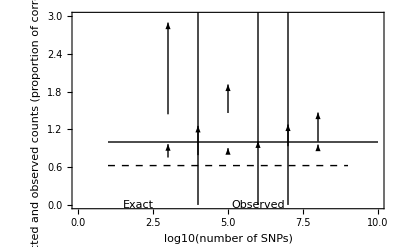

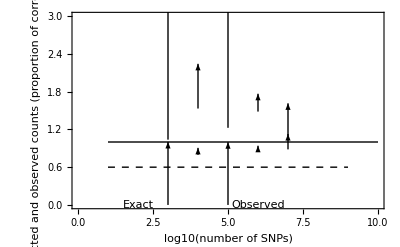

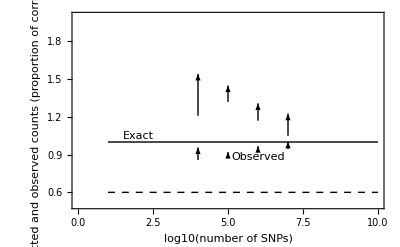

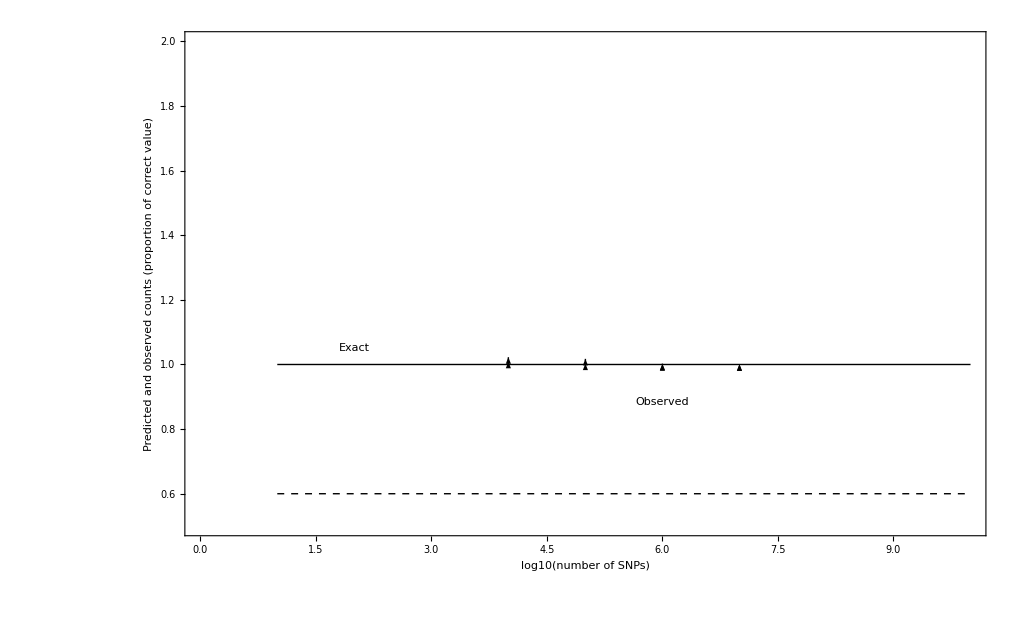

```mathematica
plotDataS=Map[confInt,outS[[1;;6]]]/1000000;
barsmin2=Table[{arrstylelow, Arrow[{{Log10[sizes⟦i⟧],plotDataS[[i,3]]/plotDataS[[i,2]]}, {Log10[sizes⟦i⟧],plotDataS[[i,4]]/plotDataS[[i,2]]}}]},{i,1,Length[plotDataS]}];
barsmax2=Table[{arrstyleup,Arrow[{{Log10[sizes⟦i⟧],plotDataS[[i,5]]/plotDataS[[i,2]]}, {Log10[sizes⟦i⟧],plotDataS[[i,6]]/plotDataS[[i,2]]}}]},{i,1,Length[plotDataS]}];

ListPlot[{Table[{x,1},{x,1,10}],Table[{x,plotDataS⟦2,1⟧/plotDataS⟦2,2⟧},{x,1,9}]},Joined->True,Epilog->{Join[barsmin2,barsmax2],Style[Text["Observed",{6,1.01*plotDataS[[1,1]]}],13],Style[Text["Exact",{2,1.05*plotDataS[[1,2]]}],13]}  ,PlotRange->{.0,3},PlotStyle->{Black,{Dashed,Black}},Frame->{True,True,False,False},FrameStyle->Directive[13],FrameLabel->{"log10(number of SNPs)","Predicted and observed counts (proportion of correct value)" }]
```

```mathematica
(*Simulation for the effect of finite data: Take a smooth SFS; Poisson Random field sample it; for each SNP in the set and each bootstrap iteration; actually perform a Hypergeometric downsampling. Assumes a monotonicity constraint*)

extrapolateBootMonoHypergeo[sampsize_,popsize_,max_,cut_,nboot_,totsnp_,propmon_]:=Module[{b,tot,pop,poisson,nmono,bloc,poploc,bchp},
pop={Table[10/(n+1/10),{n,0,max}]};
pop=pop/Apply[Plus,Flatten[pop][[2;;]]]*totsnp;
(*now poissonify*)
poisson={Map[RandomInteger[PoissonDistribution[#]]&,pop[[1]]]};
nmono=Round[propmon*popsize];

monotony=SparseArray[{Band[{1,1}]->1,Band[{1,2}]->-1},{nmono+1,popsize}]⟦2;;,1;;⟧; (*We do not want to impose a constraint on zerotons, hence the 2;;*)
monoconst=Table[{0,1},{it,1 ,nmono}];
If[popsize==sampsize,(*Then project down rather than extrapolate.*)
bloc=mat[max,popsize];
poploc=poisson;
sub=Transpose[Dot[bloc,Transpose[poploc]]]; 


tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];

If[popsize<sampsize,  (*Then project down rather than extrapolate.*)  
b=mat[max,sampsize];
bchp=b[[2;;,2;;]];
bloc=mat[sampsize,popsize];
poploc=Transpose[Dot[b,Transpose[poisson]]]; 

sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];


b=mat[max,popsize];


bloc=mat[popsize,sampsize];
(*projection matrix without singletons*)
bchp=bloc[[2;;,2;;]];
(*The SFS may have float entries. We correct this by drawing a Poisson number from each bin.*)
poploc=Transpose[Dot[b,Transpose[poisson]]];

sub=HGDownsample[poploc⟦1⟧,sampsize];
(*Build maximum likelihood solution with noise*)


(*subcoarse=poisson[[1;;cut+1]];*)
subcoarse=coarsenSFS[{sub}, cut];
bchpCoarse=coarsenMAT[bchp,cut];


obs=Apply[Plus,subcoarse[[2;;]]];

 
(*pop={Table[10/(n+1/10),{n,0,popsize}]};

sub=Transpose[Dot[b,Transpose[pop]]];*)
c=Table[1,{i,1,popsize}];

bmono=Join[bchpCoarse,monotony];
cmono=Join[N[Table[{subcoarse[[i]],0},{i,2,Length[subcoarse]}],100],monoconst];


sol=Check[c.LinearProgramming[c,bmono,cmono,Method->"RevisedSimplex"],"Err"];

solmin=Check[c.LinearProgramming[-c,bmono,cmono,Method->"RevisedSimplex"],"Err"];

exact=Apply[Plus,poploc[[1,2;;]]];
ret1={obs,sol,exact,solmin};

boots={};
For[i=1,i≤nboot,i++,
sub=HGDownsample[poploc⟦1⟧,sampsize];;

subcoarse=coarsenSFS[{sub}, cut];


c=Table[1,{i,1,popsize}];
cmono=Join[N[Table[{subcoarse[[i]],0},{i,2,Length[subcoarse]}],100],monoconst];
sol=Check[c.LinearProgramming[c,bmono,cmono,Method->"RevisedSimplex"],0];

solmin=Check[c.LinearProgramming[-c,bmono,cmono,Method->"RevisedSimplex"],1000*exact];

AppendTo[boots,{sol,solmin}];
];



Return[{ret1,boots}]
]
```

```mathematica
(*This step is a bit slower, because we are performing bootstrap over a wide range of difficult extrapolations*)
start=50
target=1000
max=1000
nboot=40
fmono=0.1

failnum=max;
smallestlog=3
largestlog=8
sizes=Table[10^nsnp,{nsnp,smallestlog,largestlog}]
SeedRandom[1]
outM=ParallelTable[Module[{locfail,nofail,step,offset,cut,success,failnum,old,out},success=True;cut=1;nofail=True;step=4;failnum=max;Catch[While[nofail,Print[" Log10(snps) ",nsnp," bins ",cut];If[cut≥failnum (*already visited and failed*),cut-=step(*go back one step*);If[step==1,Throw[out],step=step/2] ;(*take a smaller step*),(*Not tried yet: try it*) 
Check[out=extrapolateBootMonoHypergeo[start,target,max,cut,nboot,10^nsnp,fmono],(*it failed*)success=False;failnum=Min[cut,failnum];If[step==1,Throw[out],cut-=step;step=step/2]If [success,old=out,out=old;success=True];]];cut+=step]]],{nsnp,3,8}];
```

```mathematica
SeedRandom[1]
extrapolateBootMonoHypergeo[start,target,max,cut,nboot,10^nsnp,0]
```

{{6325,8089.7618800701819995858640329096895268540856035536346934709575978783546266634530201336556584143,9918,22762.875332945479143804399980541794615813405241679036310833632663814319252444545759653350153285},{{7939.20306770651552636761612519558166583831363393059109751720596027734037444070356865350663265804,22203.736374749866704340650700592332395917263134432756375163423205961281117712669763396974680504},{7901.97158350891450501464989823715894445673280573659348605984626388539509696802924588822275728197,21956.109667086577854878418264290690788195272976711675799468101741950785422778019403118117647942}}}

```mathematica
SeedRandom[1]
extrapolateBootMonoHypergeo[start,target,max,cut,nboot,10^nsnp,.1]
```

{{6325,8794.93503308783611462452892059504288171202209129887885987720117784228383749644268235006193683,9918,18590.78797840713546658697702045234848384960844094235930757754587351419838356293969336815806},{{8610.3496581900217981595804241224726627653219448832442951152355290027037655800623670531981559,18203.06447418958960147841714353363176530296194127132792706016608164098265984444669086637894},{8573.6874002425010787115474409721268462641712167238737181438745141867726802901924486812962818,17864.852972012107308621214073948783185201800553851439739778512446195852486243876471400208902}}}

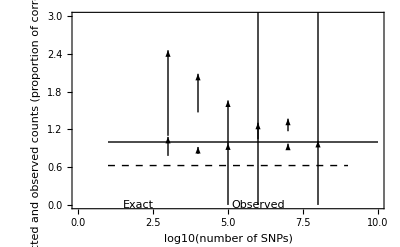

```mathematica
plotDataS=Map[confInt,outM[[1;;6]]]/1000000;
barsmin2=Table[{arrstylelow, Arrow[{{Log10[sizes⟦i⟧],plotDataS[[i,3]]/plotDataS[[i,2]]}, {Log10[sizes⟦i⟧],plotDataS[[i,4]]/plotDataS[[i,2]]}}]},{i,1,Length[plotDataS]}];
barsmax2=Table[{arrstyleup,Arrow[{{Log10[sizes⟦i⟧],plotDataS[[i,5]]/plotDataS[[i,2]]}, {Log10[sizes⟦i⟧],plotDataS[[i,6]]/plotDataS[[i,2]]}}]},{i,1,Length[plotDataS]}];

ListPlot[{Table[{x,1},{x,1,10}],Table[{x,plotDataS⟦2,1⟧/plotDataS⟦2,2⟧},{x,1,9}]},Joined->True,Epilog->{Join[barsmin2,barsmax2],Style[Text["Observed",{6,1.01*plotDataS[[1,1]]}],13],Style[Text["Exact",{2,1.05*plotDataS[[1,2]]}],13]}  ,PlotRange->{.0,3},PlotStyle->{Black,{Dashed,Black}},Frame->{True,True,False,False},FrameStyle->Directive[13],FrameLabel->{"log10(number of SNPs)","Predicted and observed counts (proportion of correct value)" }]
```

```mathematica
optimizecut[start_,values_,monotony_,monoconst_,c_,bchp_]:=Module[{keeptrying,step,trycut,subcoarse,bmono,cmono,sol,solmin,obs},
keeptrying=True;
step=1;(*step size by which to change the cutoff initially*)
trycut=start+step;
While[keeptrying,
trycut=trycut-step;

If[ trycut==0,Break[]];
keeptrying=False;
subcoarse=coarsenSFS[{values}, trycut];
obs=Apply[Plus,subcoarse[[2;;]]];
bchpCoarse=coarsenMAT[bchp,trycut];
bmono=Join[bchpCoarse,monotony];
cmono=Join[N[Table[{subcoarse[[i]],0},{i,2,Length[subcoarse]}],100],monoconst];

sol=Check[c.LinearProgramming[c,bmono,cmono,Method->"RevisedSimplex"],keeptrying=True];
solmin=Check[c.LinearProgramming[-c,bmono,cmono,Method->"RevisedSimplex"],keeptrying=True]];
If[Not[keeptrying],Return[{obs,sol,solmin,trycut}]];


]
extrapolateBootMonoHypergeo[sampsize_,popsize_,max_,startcut_,nboot_,totsnp_,propmon_]:=Module[{b,tot,pop,poisson,nmono,bloc,poploc,bchp,sub,monotony,monoconst,obs,exact,sol,solmin,trycut,subcoarse,boots,c,bchpCoarse,ret1},

pop={Table[10/(n+1/10),{n,0,max}]};
pop=pop/Apply[Plus,Flatten[pop][[2;;]]]*totsnp;
(*now poissonify*)
poisson={Map[RandomInteger[PoissonDistribution[#]]&,pop[[1]]]};
nmono=Round[propmon*popsize];

monotony=SparseArray[{Band[{1,1}]->1,Band[{1,2}]->-1},{nmono+1,popsize}]⟦2;;,1;;⟧; (*We do not want to impose a constraint on zerotons, hence the 2;;*)
monoconst=Table[{0,1},{it,1 ,nmono}];
If[popsize==sampsize,(*Then project down rather than extrapolate.*)
bloc=mat[max,popsize];
poploc=poisson;
sub=Transpose[Dot[bloc,Transpose[poploc]]]; 


tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];

If[popsize<sampsize,  (*Then project down rather than extrapolate.*)  
b=mat[max,sampsize];
bchp=b[[2;;,2;;]];
bloc=mat[sampsize,popsize];
poploc=Transpose[Dot[b,Transpose[poisson]]]; 

sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];


b=mat[max,popsize];


bloc=mat[popsize,sampsize];
(*projection matrix without singletons*)
bchp=bloc[[2;;,2;;]];
poploc=Round[Transpose[Dot[b,Transpose[poisson]]]];

sub=HGDownsample[poploc⟦1⟧,sampsize];
(*Build maximum likelihood solution with noise*)
(*subcoarse=poisson[[1;;cut+1]];*)
subcoarse=coarsenSFS[{sub}, startcut];
bchpCoarse=coarsenMAT[bchp,startcut];


obs=Apply[Plus,subcoarse[[2;;]]];

 
(*pop={Table[10/(n+1/10),{n,0,popsize}]};

sub=Transpose[Dot[b,Transpose[pop]]];*)
c=Table[1,{i,1,popsize}];

(*bmono=Join[bchpCoarse,monotony];
cmono=Join[N[Table[{subcoarse[[i]],0},{i,2,Length[subcoarse]}],100],monoconst];*)

(*This first run is not really useful--we keep it there for compatibility reasons.*)

(*sol=Check[c.LinearProgramming[c,bmono,cmono,Method->"RevisedSimplex"],"Err"];

solmin=Check[c.LinearProgramming[-c,bmono,cmono,Method->"RevisedSimplex"],"Err"];*)

exact=Apply[Plus,poploc[[1,2;;]]];
ret1={obs,exact};

boots=ParallelTable[
RandomSeed[i];
sub=HGDownsample[poploc⟦1⟧,sampsize];
{obs,sol,solmin,trycut}=optimizecut[startcut,sub,monotony,monoconst,c,bchp];

(*Print[N[{obs,exact,sol,solmin,trycut,nmono}]];*)
{obs,exact,sol,solmin,trycut}
,{i,1,nboot}];


Return[{ret1,boots}]
]
```

```mathematica
start=50
target=1000
max=1000
nboot=40
fmono=0.1
startcut=16;
failnum=max;
smallestlog=3
largestlog=8
sizes=Table[10^nsnp,{nsnp,smallestlog,largestlog}]
SeedRandom[1]
out50T1000=ParallelTable[extrapolateBootMonoHypergeo[start,target,max,startcut,nboot,10^nsnp,fmono],{nsnp,3,8},{fmono,{0,0.005,0.01,0.02}}];
```

```mathematica
start=50
target=100
max=100
nboot=40
fmono=0.1
startcut=16;
failnum=max;
smallestlog=3
largestlog=8
sizes=Table[10^nsnp,{nsnp,smallestlog,largestlog}]
SeedRandom[1]
out50T100=ParallelTable[extrapolateBootMonoHypergeo[start,target,max,startcut,nboot,10^nsnp,fmono],{nsnp,3,8},{fmono,{0,0.005,0.01,0.02}}];
```

```mathematica
start=50
target=200
max=200
nboot=40
fmono=0
startcut=16;
failnum=max;
smallestlog=3
largestlog=8
sizes=Table[10^nsnp,{nsnp,smallestlog,largestlog}]
SeedRandom[1]
(*Here we just run f=0*)
out50T200={Table[Print[nsnp];extrapolateBootMonoHypergeo[start,target,max,startcut,nboot,10^nsnp,fmono],{nsnp,3,8}]};
```

```mathematica
start=50
target=300
max=target
nboot=40
fmono=0
startcut=16;
failnum=max;
smallestlog=3
largestlog=8
sizes=Table[10^nsnp,{nsnp,smallestlog,largestlog}]
SeedRandom[1]
(*Here we just run f=0*)
out50T300={Table[Print[nsnp];extrapolateBootMonoHypergeo[start,target,max,startcut,nboot,10^nsnp,fmono],{nsnp,3,8}]};
Save["~/Dropbox/capture_recapture/mathematicascripts/outputs/mono_size50T300",out50T300]
start=50
target=350
max=350
nboot=40
fmono=0
startcut=16;
failnum=max;
smallestlog=3
largestlog=8
sizes=Table[10^nsnp,{nsnp,smallestlog,largestlog}]
SeedRandom[1]
(*Here we just run f=0*)
out50T350={Table[Print[nsnp];extrapolateBootMonoHypergeo[start,target,max,startcut,nboot,10^nsnp,fmono],{nsnp,3,8}]};
Save["~/Dropbox/capture_recapture/mathematicascripts/outputs/mono_size50T350",out50T350]
```

50

300

300

40

0

3

8

{1000,10000,100000,1000000,10000000,100000000}

3

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

4

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

5

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

6

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

7

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

8

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

50

350

350

40

0

3

8

{1000,10000,100000,1000000,10000000,100000000}

3

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

4

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

5

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

6

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

7

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

8

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming :: lpsnf will be suppressed during this calculation.

```mathematica
start=50
target=400
max=400
nboot=40
fmono=0.1
startcut=16;
failnum=max;
smallestlog=3
largestlog=8
sizes=Table[10^nsnp,{nsnp,smallestlog,largestlog}]
SeedRandom[1]
out50T400=ParallelTable[extrapolateBootMonoHypergeo[start,target,max,startcut,nboot,10^nsnp,fmono],{nsnp,3,8},{fmono,{0,0.005,0.01,0.02}}];
```

```mathematica
Save["~/Dropbox/capture_recapture/mathematicascripts/outputs/mono_size50T200",out50T200]
```

```mathematica
(*Save to file.*)
Save["~/Dropbox/capture_recapture/mathematicascripts/outputs/mono_size50T100",out50T100]
Save["~/Dropbox/capture_recapture/mathematicascripts/outputs/mono_size50T400",out50T400]
Save["~/Dropbox/capture_recapture/mathematicascripts/outputs/mono_size50T1000",out50T1000]
```

```mathematica
(*Load from file if exists*)
Get["~/Dropbox/capture_recapture/mathematicascripts/outputs/mono_size50T100"];
Get["~/Dropbox/capture_recapture/mathematicascripts/outputs/mono_size50T400"];
Get["~/Dropbox/capture_recapture/mathematicascripts/outputs/mono_size50T1000"];
```

```mathematica
(*get a confidence interval from the output!*)
confInt2[out_]:=Module[{start,exact,max,min},start=Mean[out[[2,1;;,1]]];exact=out[[1,2]]; minmin=Quantile[out[[2,1;;,3]],0.025]; minmax=Quantile[out[[2,1;;,3]],0.975];maxmax=Quantile[out[[2,1;;,4]],.975];maxmin=Quantile[out[[2,1;;,4]],.025];{start,exact,minmin,minmax,maxmin,maxmax}]

dattoCI[dat_,fslice_]:=Map[confInt2,dat[[1;;,fslice]]]




plot50T100=Table[N[dattoCI[out50T100,i]],{i,1,4}];
plot50T200=Table[N[dattoCI[Transpose[out50T200],i]],{i,1,1}];
plot50T300=Table[N[dattoCI[Transpose[out50T300],i]],{i,1,1}];
plot50T350=Table[N[dattoCI[Transpose[out50T350],i]],{i,1,1}];
plot50T400=Table[N[dattoCI[out50T400,i]],{i,1,4}];
plot50T1000=Table[N[dattoCI[out50T1000,i]],{i,1,4}];
```

```mathematica
offsetscale=-0.1;
colors={Red, Purple,Blue, Gray}
plotout[plotDatavec_,sizes_,range_]:=Module[{barsmin2,barsmax2,plotDataS,enum,nExt,offsetnum,means},
nExt=Length[plotDatavec];
allbarsmin={};
allbarsmax={};
means={};
For[enum=1,enum≤nExt,enum++,
plotDataS=plotDatavec⟦enum⟧;
offsetnum=-nExt/2+enum;
AppendTo[allbarsmin,Table[{colors⟦enum⟧,arrstylelow, Arrow[{{Log10[sizes⟦i⟧]+offsetnum*offsetscale,plotDataS[[i,3]]/plotDataS[[i,2]]}, {Log10[sizes⟦i⟧]+offsetnum*offsetscale,plotDataS[[i,4]]/plotDataS[[i,2]]}}]},{i,1,Length[plotDataS]}]];
AppendTo[allbarsmax,Table[{colors⟦enum⟧,arrstyleup,Arrow[{{Log10[sizes⟦i⟧]+offsetnum*offsetscale,plotDataS[[i,5]]/plotDataS[[i,2]]}, {Log10[sizes⟦i⟧]+offsetnum*offsetscale,plotDataS[[i,6]]/plotDataS[[i,2]]}}]},{i,1,Length[plotDataS]}]];
AppendTo[means,plotDataS⟦2,1⟧/plotDataS⟦2,2⟧];
];
(*observed values*)

ListPlot[Join[{Table[{x,1},{x,2,8}]},Table[Table[{x,means⟦i⟧},{x,2,8}],{i,1,nExt}]],Joined->True,Epilog->{Join[allbarsmin,allbarsmax],Style[Text["Observed",{6,1.01*plotDataS[[1,1]]}],13],Style[Text["Exact",{2,1.05*plotDataS[[1,2]]}],13]}  ,PlotRange->range,PlotStyle->Join[{Black},Table[{Dashed,colors⟦i⟧},{i,1,nExt}]],Frame->{True,True,False,False},FrameStyle->Directive[13],FrameLabel->{"log10(number of SNPs)","Predicted and observed counts (proportion of correct value)" }]]
```

{RGBColor[1,0,0],RGBColor[0.5,0,0.5],RGBColor[0,0,1],GrayLevel[0.5]}

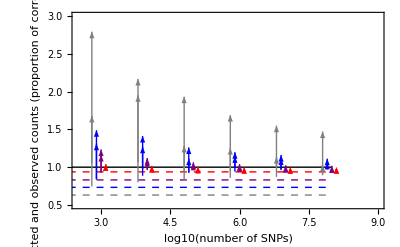

```mathematica
plotout[{plot50T100⟦1⟧,plot50T200⟦1⟧,plot50T400⟦1⟧,plot50T1000⟦1⟧},sizes,{{2.5,9},{.5,3}}]
```

```mathematica
(*Add a run with infinite data*)
extrapolateMonoInfinite[sampsize_,popsize_,max_,startcut_,nboot_,totsnp_,propmon_]:=Module[{b,tot,poisson,nmono,bloc,poploc,bchp,sub,monotony,monoconst,obs,exact,sol,solmin,trycut,subcoarse,boots,c,bchpCoarse,ret1,pop},

pop={Table[10/(n+1/10),{n,0,max}]};
pop=pop/Apply[Plus,Flatten[pop][[2;;]]]*totsnp;
(*Poisson= pop for infinite data*)
poisson=pop;
nmono=Round[propmon*popsize];

monotony=SparseArray[{Band[{1,1}]->1,Band[{1,2}]->-1},{nmono+1,popsize}]⟦2;;,1;;⟧; (*We do not want to impose a constraint on zerotons, hence the 2;;*)
monoconst=Table[{0,1},{it,1 ,nmono}];
If[popsize==sampsize,(*Then project down rather than extrapolate.*)
bloc=mat[max,popsize];
poploc=poisson;
sub=Transpose[Dot[bloc,Transpose[poploc]]]; 


tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];

If[popsize<sampsize,  (*Then project down rather than extrapolate.*)  
b=mat[max,sampsize];
bchp=b[[2;;,2;;]];
bloc=mat[sampsize,popsize];
poploc=Transpose[Dot[b,Transpose[poisson]]]; 

sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];


b=mat[max,popsize];


bloc=mat[popsize,sampsize];
(*projection matrix without singletons*)
bchp=bloc[[2;;,2;;]];
poploc=Transpose[Dot[b,Transpose[poisson]]];

exact=Apply[Plus, poploc⟦1,2;;⟧];

sub=Transpose[Dot[bloc,Transpose[poploc]]];

(*Build maximum likelihood solution with noise*)


(*subcoarse=poisson[[1;;cut+1]];*)

subcoarse=coarsenSFS[sub, startcut];


bchpCoarse=coarsenMAT[bchp,startcut];


obs=Apply[Plus,subcoarse[[2;;]]];

c=Table[1,{i,1,popsize}];

bmono=Join[bchpCoarse,monotony];
cmono=Join[N[Table[{subcoarse[[i]],0},{i,2,Length[subcoarse]}],100],monoconst];

(*This first run is not really useful--we keep it there for compatibility reasons.*)

sol=Check[c.LinearProgramming[c,bmono,cmono,Method->"RevisedSimplex"],"Err"];

solmin=Check[c.LinearProgramming[-c,bmono,cmono,Method->"RevisedSimplex"],"Err"];


ret1={obs,exact,sol,solmin};

boots={};
For[i=1,i≤nboot,i++,
sub=HGDownsample[poploc⟦1⟧,sampsize];
{obs,sol,solmin,trycut}=optimizecut[startcut,sub,monotony,monoconst,c,bchp];

(*Print[N[{obs,exact,sol,solmin,trycut,nmono}]];*)
AppendTo[boots,{obs,exact,sol,solmin,trycut}];
];



Return[{ret1,boots}]
]
```

```mathematica
start=50;
target=1000;
max=target;
nboot=0;
fmono=0.0;
startcut=49;
totsnp=100;
inf50T1000=ParallelTable[N[extrapolateMonoInfinite[start,target,max,startcut,nboot,totsnp,fmono]],{fmono,{0,0.005,0.01,0.02}}]
```

{{{61.0951,100.,94.9884,105.117},{}},{{61.0951,100.,95.4084,103.56},{}},{{61.0951,100.,95.4907,102.647},{}},{{61.0951,100.,96.1199,102.483},{}}}

```mathematica
start=50;
target=200;
max=target;
nboot=0;
fmono=0.0;
startcut=49;
totsnp=100;
inf50T200=ParallelTable[N[extrapolateMonoInfinite[start,target,max,startcut,nboot,totsnp,fmono]],{fmono,{0,0.005,0.01,0.02}}]
```

{{{77.4879,100.,99.984,100.013},{}},{{77.4879,100.,99.984,100.011},{}},{{77.4879,100.,99.9928,100.011},{}},{{77.4879,100.,99.9931,100.006},{}}}

```mathematica
start=50;
target=400;
max=target;
nboot=0;
fmono=0.0;
startcut=49;
totsnp=100;
inf50T400=ParallelTable[N[extrapolateMonoInfinite[start,target,max,startcut,nboot,totsnp,fmono]],{fmono,{0,0.005,0.01,0.02}}]

start=50;
target=100;
max=target;
nboot=0;
fmono=0.0;
startcut=49;
totsnp=100;
inf50T100=ParallelTable[N[extrapolateMonoInfinite[start,target,max,startcut,nboot,totsnp,fmono]],{fmono,{0,0.005,0.01,0.02}}]
```

{{{69.5127,100.,99.4772,100.504},{}},{{69.5127,100.,99.4772,100.228},{}},{{69.5127,100.,99.7002,100.226},{}},{{69.5127,100.,99.77,100.181},{}}}

{{{87.3881,100.,100.,100.},{}},{{87.3881,100.,100.,100.},{}},{{87.3881,100.,100.,100.},{}},{{87.3881,100.,100.,100.},{}}}

{{{87.3881,100.,100.,100.},{}},{{77.4879,100.,99.984,100.013},{}},{{69.5127,100.,99.4772,100.504},{}},{{61.0951,100.,94.9884,105.117},{}}}

```mathematica
offsetscale=0.1;
colors={Orange,Red, Purple,Blue}
plotout[plotDatavec_,sizes_,range_,inf_]:=
Module[{barsmin2,barsmax2,plotDataS,enum,nExt,offsetnum,means},
nExt=Length[plotDatavec];
allbarsmin={};
allbarsmax={};
means={};
For[enum=1,enum≤nExt,enum++,
plotDataS=plotDatavec⟦enum⟧;
offsetnum=-nExt/2+enum;
AppendTo[allbarsmin,Table[{colors⟦enum⟧,arrstylelow, Arrow[{{Log10[sizes⟦i⟧]+offsetnum*offsetscale-0.5*offsetscale,plotDataS[[i,3]]/plotDataS[[i,2]]}, {Log10[sizes⟦i⟧]+offsetnum*offsetscale-0.5*offsetscale,plotDataS[[i,4]]/plotDataS[[i,2]]}}]},{i,1,Length[plotDataS]}]];
AppendTo[allbarsmax,Table[{colors⟦enum⟧,arrstyleup,Arrow[{{Log10[sizes⟦i⟧]+offsetnum*offsetscale-0.5*offsetscale,plotDataS[[i,5]]/plotDataS[[i,2]]}, {Log10[sizes⟦i⟧]+offsetnum*offsetscale-0.5*offsetscale,plotDataS[[i,6]]/plotDataS[[i,2]]}}]},{i,1,Length[plotDataS]}]];
AppendTo[means,plotDataS⟦2,1⟧/plotDataS⟦2,2⟧];
];
(*Put infinite-limit data*)

infOffset=1;
AppendTo[allbarsmin,Table[offsetnum=-nExt/2+enum-0.5;{colors⟦enum⟧,arrstylelow,Arrow[{{Log10[sizes⟦-1⟧]+offsetnum*offsetscale+infOffset,inf[[enum,1,3]]/inf[[enum,1,2]]}, {Log10[sizes⟦-1⟧]+offsetnum*offsetscale+infOffset,inf[[enum,1,3]]/inf[[enum,1,2]]+10^-9 (*pseudocount to avoid size zero drawing*)}}]},{enum,1,nExt}]];
AppendTo[allbarsmax,Table[offsetnum=-nExt/2+enum-0.5;{colors⟦enum⟧,arrstyleup,Arrow[{{Log10[sizes⟦-1⟧]+offsetnum*offsetscale+infOffset,inf[[enum,1,4]]/inf[[enum,1,2]]}, {Log10[sizes⟦-1⟧]+offsetnum*offsetscale+infOffset,inf[[enum,1,4]]/inf[[enum,1,2]]+10^-9}}]},{enum,1,nExt}]];

ListPlot[Join[{Table[{x,1},{x,2,8.2,.1}],Table[{x,1},{x,8.8,9.2,.1}]},Table[Table[{x,means⟦i⟧},{x,2,8.2,.1}],{i,1,nExt}],Table[Table[{x,means⟦i⟧},{x,8.8,9.2,.1}],{i,1,nExt} ]],Joined->True,Epilog->{Join[allbarsmin,allbarsmax],Style[Text["Observed",{6,1.01*plotDataS[[1,1]]}],13],Style[Text["Exact",{2,1.05*plotDataS[[1,2]]}],13]}  ,PlotRange->range,PlotStyle->Join[{Black,Black},Table[{Dashed,colors⟦i⟧},{i,1,nExt}],Table[{Dashed,colors⟦i⟧},{i,1,nExt}]],Frame->{True,True,False,False},FrameStyle->Directive[13],FrameTicks->{{{3,Superscript[10,3]},{4,Superscript[10,4]},{5,Superscript[10,5]},{6,Superscript[10,6]},{7,Superscript[10,7]},{8,Superscript[10,8]},{9,∞}},Automatic},FrameLabel->{"number of SNPs","Relative confidence interval" },BaseStyle->{Large,FontFamily->"Arial"}]]
```

{RGBColor[1,0.5,0],RGBColor[1,0,0],RGBColor[0.5,0,0.5],RGBColor[0,0,1]}

{{{87.3881,100.,100.,100.},{}},{{77.4879,100.,99.984,100.013},{}},{{69.5127,100.,99.4772,100.504},{}},{{61.0951,100.,94.9884,105.117},{}}}

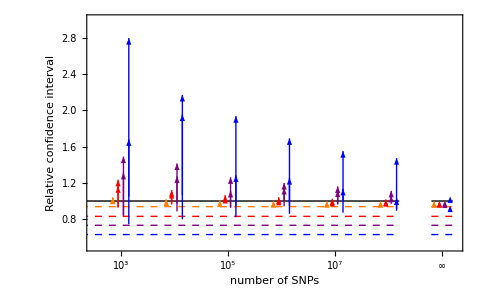

```mathematica
infNoF={inf50T100⟦1⟧,inf50T200⟦1⟧,inf50T400⟦1⟧,inf50T1000⟦1⟧}
Nexpplot=plotout[{plot50T100⟦1⟧,plot50T200⟦1⟧,plot50T400⟦1⟧,plot50T1000⟦1⟧},sizes,{{2.5,9.25},{.5,3}},infNoF]
```

```mathematica
Export["~/Dropbox/capture_recapture/figures/LvsNn.pdf",Nexpplot]
Export["~/Dropbox/capture_recapture/figures/LvsNn.eps",Nexpplot]
```

~/Dropbox/capture_recapture/figures/LvsNn.pdf

~/Dropbox/capture_recapture/figures/LvsNn.eps